```mathematica
Медленные сортировки
```

```mathematica
Insort:=Import["/Users/kuleshovladimir/Desktop/Programming/Sorts/Insertion sort/Insertion sort.csv", "Data"]
```

```mathematica
Bubsort:=Import["/Users/kuleshovladimir/Desktop/Programming/Sorts/Bubble sort/Bubble sort.csv", "Data"]
```

```mathematica
Shakesort:=Import["/Users/kuleshovladimir/Desktop/Programming/Sorts/Cocktail shaking sort/Coctail shaking sort.csv", "Data"]
```

```mathematica
CountofArray:=Table[i, {i, 1, 9951, 50}]
```

```mathematica
nlmfInsort=NonlinearModelFit[Table[{CountofArray[[i]],Insort[[i]][[1]]}, {i, Length[Insort]}], c*n^α, {c, α}, n]
nlmfBubsort=NonlinearModelFit[Table[{CountofArray[[i]],Bubsort[[i]][[1]]}, {i, Length[Insort]}], c*n^α, {c, α}, n]
nlmfShakesort=NonlinearModelFit[Table[{CountofArray[[i]],Shakesort[[i]][[1]]}, {i, Length[Insort]}], c*n^α, {c, α}, n]
```

FittedModel[0.00204054 n^1.86842]

FittedModel[0.000891861 n^2.14393]

FittedModel[0.00131423 n^2.06641]

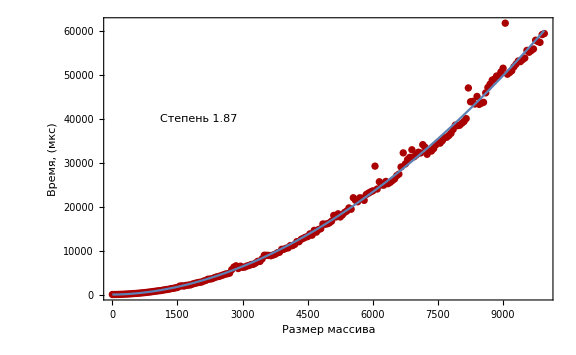

```mathematica
Show[ListPlot[Table[{CountofArray[[i]],Insort[[i]][[1]]}, {i, Length[Insort]}], PlotStyle->Darker[Red], ImageSize->Large,Frame->True,FrameStyle->Black, FrameLabel->{{HoldForm["Время, (мкс)"],None},{HoldForm["Размер массива"],HoldForm["Insertion sort"]}}, PlotRange->All,Background->White, Epilog->{ Text["Степень 1.87",{2000,40000},Background->LightRed]}], Plot[nlmfInsort[n], {n, 1, Last[CountofArray]}]]
```

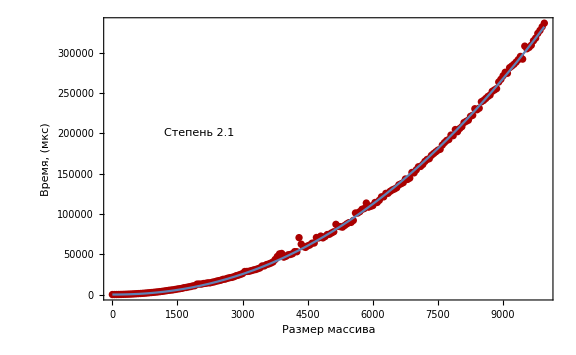

```mathematica
Show[ListPlot[Table[{CountofArray[[i]],Bubsort[[i]][[1]]}, {i, Length[Insort]}], PlotStyle->Darker[Red], ImageSize->Large,Frame->True,FrameStyle->Black, FrameLabel->{{HoldForm["Время, (мкс)"],None},{HoldForm["Размер массива"],HoldForm["Bubble sort"]}}, PlotRange->All,Background->White, Epilog->{ Text["Степень 2.1",{2000,200000},Background->LightRed]}], Plot[nlmfBubsort[n], {n, 1, Last[CountofArray]}]]
```

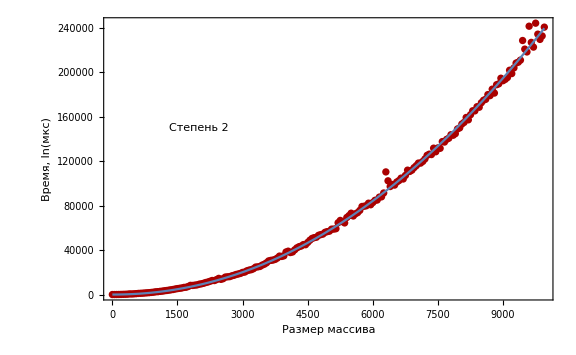

```mathematica
Show[ListPlot[Table[{CountofArray[[i]],Shakesort[[i]][[1]]}, {i, Length[Insort]}], PlotStyle->Darker[Red], ImageSize->Large,Frame->True,FrameStyle->Black, FrameLabel->{{HoldForm["Время, ln(мкс)"],None},{HoldForm["Размер массива"],HoldForm["Coctail shaking sort"]}},Background->White, PlotRange->All, Epilog->{ Text["Степень 2",{2000,150000},Background->LightRed]}], Plot[nlmfShakesort[n], {n, 1, Last[CountofArray]}]]
```

```mathematica
Разные оптимизации
```

```mathematica
BubsortO0:=Import["/Users/kuleshovladimir/Desktop/Programming/Sorts/Bubble sort/Bubble sort-O0.csv", "Data"]
BubsortO1:=Import["/Users/kuleshovladimir/Desktop/Programming/Sorts/Bubble sort/Bubble sort-O1.csv", "Data"]
BubsortO2:=Import["/Users/kuleshovladimir/Desktop/Programming/Sorts/Bubble sort/Bubble sort-O2.csv", "Data"]
BubsortO3:=Import["/Users/kuleshovladimir/Desktop/Programming/Sorts/Bubble sort/Bubble sort-O3.csv", "Data"]
```

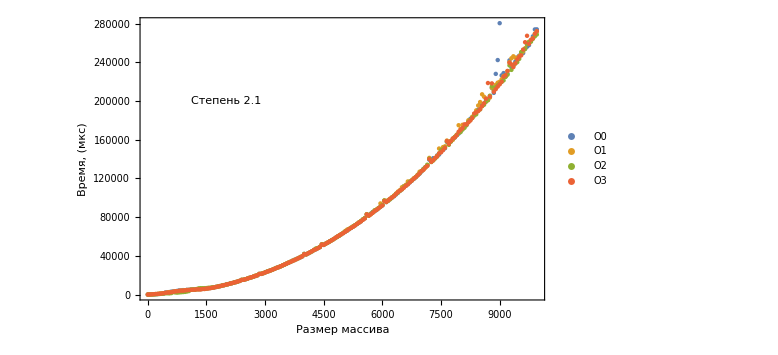

```mathematica
ListPlot[{Table[{CountofArray[[i]],BubsortO0[[i]][[1]]}, {i, Length[BubsortO0]}], Table[{CountofArray[[i]],BubsortO1[[i]][[1]]}, {i, Length[BubsortO1]}], Table[{CountofArray[[i]],BubsortO2[[i]][[1]]}, {i, Length[BubsortO2]}], Table[{CountofArray[[i]],BubsortO3[[i]][[1]]}, {i, Length[BubsortO3]}]}, ImageSize->Large,Frame->True,FrameStyle->Black, FrameLabel->{{HoldForm["Время, (мкс)"],None},{HoldForm["Размер массива"],HoldForm["Bubble sort"]}}, PlotRange->All,Background->White, Epilog->{ Text["Степень 2.1",{2000,200000},Background->LightRed]}, PlotLegends->{"O0", "O1", "O2", "O3"}]
```

```mathematica
Быстрые сортировки
```

```mathematica
MergeSort:=Import["/Users/kuleshovladimir/Desktop/Programming/Sorts/Merge sort.cpp/Merge sort.csv","Data"]
```

Power::infy: Infinite expression 1/0 encountered.

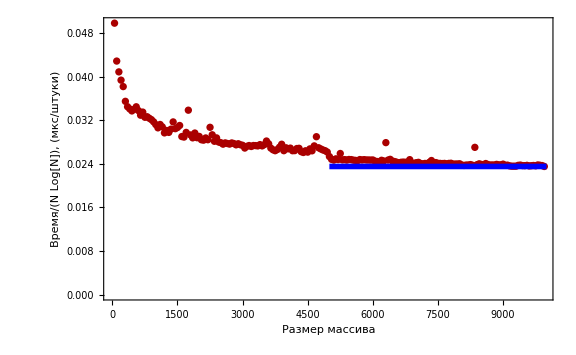

```mathematica
ListPlot[Table[{CountofArray[[i]],(MergeSort[[i]][[1]])/(CountofArray[[i]]*Log[CountofArray[[i]]])}, {i, Length[Insort]}], PlotStyle->Darker[Red], ImageSize->Large,Frame->True,FrameStyle->Black, FrameLabel->{{HoldForm["(:0412:0440:0435:043c:044f)/(N Log[N]), ((:043c:043a:0441)/(:0448:0442:0443:043a:0438))"],None},{HoldForm["Размер массива"],HoldForm["Merge sort"]}},Background->White, PlotRange->All, Epilog->{ Text["Степень 2",{2000,150000},Background->LightRed], {Blue,Thickness[0.007], Line[{{5000, 0.023536291233300574}, {10000, 0.023536291233300574}}]}}]
```

```mathematica
HeapSort:=Import["/Users/kuleshovladimir/Desktop/Programming/Sorts/Heap sort/Heap sort.csv", "Data"]
```

Power::infy: Infinite expression 1/0 encountered.

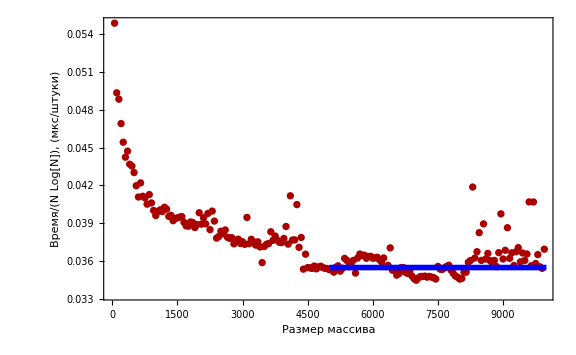

```mathematica
ListPlot[Table[{CountofArray[[i]],(HeapSort[[i]][[1]])/(CountofArray[[i]]*Log[CountofArray[[i]]])}, {i, Length[Insort]}], PlotStyle->Darker[Red], ImageSize->Large,Frame->True,FrameStyle->Black, FrameLabel->{{HoldForm["(:0412:0440:0435:043c:044f)/(N Log[N]), ((:043c:043a:0441)/(:0448:0442:0443:043a:0438))"],None},{HoldForm["Размер массива"],HoldForm["Heap sort"]}},Background->White, PlotRange->All,Epilog->{ {Blue,Thickness[0.007], Line[{{5000, 0.0355}, {10000, 0.0355}}]}}]
```

```mathematica
QuickSort:=Import["/Users/kuleshovladimir/Desktop/Programming/Sorts/Quick sort/Quick sort.csv", "Data"]
```

Power::infy: Infinite expression 1/0 encountered.

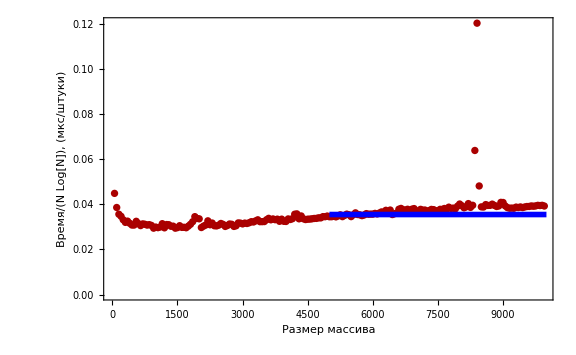

```mathematica
ListPlot[Table[{CountofArray[[i]],(QuickSort[[i]][[1]])/(CountofArray[[i]]*Log[CountofArray[[i]]])}, {i, Length[Insort]}], PlotStyle->Darker[Red], ImageSize->Large,Frame->True,FrameStyle->Black, FrameLabel->{{HoldForm["(:0412:0440:0435:043c:044f)/(N Log[N]), ((:043c:043a:0441)/(:0448:0442:0443:043a:0438))"],None},{HoldForm["Размер массива"],HoldForm["Quick sort"]}},Background->White, PlotRange->All,Epilog->{ {Blue,Thickness[0.007], Line[{{5000, 0.0355}, {10000, 0.0355}}]}}]
```

```mathematica
Сравнение сортировок
```

```mathematica
ListPlot[{Table[{CountofArray[[i]],Bubsort[[i]][[1]]}, {i, Length[Insort]}], Table[{CountofArray[[i]],Insort[[i]][[1]]}, {i, Length[Insort]}], Table[{CountofArray[[i]],Shakesort[[i]][[1]]}, {i, Length[Insort]}], Table[{CountofArray[[i]],MergeSort[[i]][[1]]}, {i, Length[Insort]}], Table[{CountofArray[[i]],HeapSort[[i]][[1]]}, {i, Length[Insort]}], Table[{CountofArray[[i]],QuickSort[[i]][[1]]}, {i, Length[Insort]}]}, ImageSize->Large,Frame->True,FrameStyle->Black, FrameLabel->{{HoldForm["Время, (мкс)"],None},{HoldForm["Размер массива"],None}}, PlotRange->All,Background->White, PlotLabels->{"Bubble sort", "Insert sort", "Coctail shaking sort", "Merge sort", "Heap sort", "Quick sort"}]
```

-Graphics-